```mathematica
arr = {{"1.in",10000,10000,100,1183271,1973019,1667858,1896925,2084523,1970848,2534624},{"2.in",10000,12742,100,1347459,2171161,1882561,2073984,2415687,2381198,3034866},{"3.in",10000,16237,100,1720593,2561601,2175386,2307347,2622522,2763595,3539244},{"4.in",10000,20691,100,1874292,2695989,2390626,2500207,2850192,2960773,3795149},{"5.in",10000,26365,100,2143126,2924183,2570942,2690887,3035701,3191286,3934234},{"6.in",10000,33597,100,2428087,3113106,2816330,2895176,3229580,3477576,4158447},{"7.in",10000,42811,100,2563758,3287805,2986554,3030880,3470426,3745152,4338199},{"8.in",10000,54553,100,2775356,3536922,3302526,3219807,3700801,4006220,4688955},{"9.in",10000,69516,100,3157069,3908516,3585477,3524235,4091808,4405015,5107174},{"10.in",10000,88582,100,3549179,4249697,3984995,3915178,4331413,4816740,5430285},{"11.in",10000,112877,100,4033886,4691479,4295760,4352458,4744089,5359519,6061056},{"12.in",10000,143836,100,4729622,5434109,5124605,4909557,5473994,6014711,7089776},{"13.in",10000,183286,100,5365548,6292916,5917205,5729512,6321414,6866827,7737154},{"14.in",10000,233556,100,6387629,7295437,7028013,6673580,7250740,7854463,8787380},{"15.in",10000,297613,100,7652805,8488593,8155715,7803503,8382280,9077989,10038152},{"16.in",10000,379239,100,8956053,9839742,9446346,9124127,9803096,10471550,11418456},{"17.in",10000,483252,100,10603086,11591953,11201528,10823004,11450304,12225425,13294717},{"18.in",10000,615793,100,12736939,13697909,13280922,13180311,13544086,14355260,15503093},{"19.in",10000,784685,100,15317093,16357884,16077947,15484613,16203115,17044329,18333629},{"20.in",10000,999899,100,18435257,19690749,19278313,18873630,19537714,20380358,21791619}
};
```

```mathematica
list = Array[{arr[[#1,3]],arr[[#1,#2+4]]}&,{Length[arr],7}]
```

{{{10000,1183271},{10000,1973019},{10000,1667858},{10000,1896925},{10000,2084523},{10000,1970848},{10000,2534624}},{{12742,1347459},{12742,2171161},{12742,1882561},{12742,2073984},{12742,2415687},{12742,2381198},{12742,3034866}},{{16237,1720593},{16237,2561601},{16237,2175386},{16237,2307347},{16237,2622522},{16237,2763595},{16237,3539244}},{{20691,1874292},{20691,2695989},{20691,2390626},{20691,2500207},{20691,2850192},{20691,2960773},{20691,3795149}},{{26365,2143126},{26365,2924183},{26365,2570942},{26365,2690887},{26365,3035701},{26365,3191286},{26365,3934234}},{{33597,2428087},{33597,3113106},{33597,2816330},{33597,2895176},{33597,3229580},{33597,3477576},{33597,4158447}},{{42811,2563758},{42811,3287805},{42811,2986554},{42811,3030880},{42811,3470426},{42811,3745152},{42811,4338199}},{{54553,2775356},{54553,3536922},{54553,3302526},{54553,3219807},{54553,3700801},{54553,4006220},{54553,4688955}},{{69516,3157069},{69516,3908516},{69516,3585477},{69516,3524235},{69516,4091808},{69516,4405015},{69516,5107174}},{{88582,3549179},{88582,4249697},{88582,3984995},{88582,3915178},{88582,4331413},{88582,4816740},{88582,5430285}},{{112877,4033886},{112877,4691479},{112877,4295760},{112877,4352458},{112877,4744089},{112877,5359519},{112877,6061056}},{{143836,4729622},{143836,5434109},{143836,5124605},{143836,4909557},{143836,5473994},{143836,6014711},{143836,7089776}},{{183286,5365548},{183286,6292916},{183286,5917205},{183286,5729512},{183286,6321414},{183286,6866827},{183286,7737154}},{{233556,6387629},{233556,7295437},{233556,7028013},{233556,6673580},{233556,7250740},{233556,7854463},{233556,8787380}},{{297613,7652805},{297613,8488593},{297613,8155715},{297613,7803503},{297613,8382280},{297613,9077989},{297613,10038152}},{{379239,8956053},{379239,9839742},{379239,9446346},{379239,9124127},{379239,9803096},{379239,10471550},{379239,11418456}},{{483252,10603086},{483252,11591953},{483252,11201528},{483252,10823004},{483252,11450304},{483252,12225425},{483252,13294717}},{{615793,12736939},{615793,13697909},{615793,13280922},{615793,13180311},{615793,13544086},{615793,14355260},{615793,15503093}},{{784685,15317093},{784685,16357884},{784685,16077947},{784685,15484613},{784685,16203115},{784685,17044329},{784685,18333629}},{{999899,18435257},{999899,19690749},{999899,19278313},{999899,18873630},{999899,19537714},{999899,20380358},{999899,21791619}}}

```mathematica
mat = Transpose[list]
```

{{{10000,1183271},{12742,1347459},{16237,1720593},{20691,1874292},{26365,2143126},{33597,2428087},{42811,2563758},{54553,2775356},{69516,3157069},{88582,3549179},{112877,4033886},{143836,4729622},{183286,5365548},{233556,6387629},{297613,7652805},{379239,8956053},{483252,10603086},{615793,12736939},{784685,15317093},{999899,18435257}},{{10000,1973019},{12742,2171161},{16237,2561601},{20691,2695989},{26365,2924183},{33597,3113106},{42811,3287805},{54553,3536922},{69516,3908516},{88582,4249697},{112877,4691479},{143836,5434109},{183286,6292916},{233556,7295437},{297613,8488593},{379239,9839742},{483252,11591953},{615793,13697909},{784685,16357884},{999899,19690749}},{{10000,1667858},{12742,1882561},{16237,2175386},{20691,2390626},{26365,2570942},{33597,2816330},{42811,2986554},{54553,3302526},{69516,3585477},{88582,3984995},{112877,4295760},{143836,5124605},{183286,5917205},{233556,7028013},{297613,8155715},{379239,9446346},{483252,11201528},{615793,13280922},{784685,16077947},{999899,19278313}},{{10000,1896925},{12742,2073984},{16237,2307347},{20691,2500207},{26365,2690887},{33597,2895176},{42811,3030880},{54553,3219807},{69516,3524235},{88582,3915178},{112877,4352458},{143836,4909557},{183286,5729512},{233556,6673580},{297613,7803503},{379239,9124127},{483252,10823004},{615793,13180311},{784685,15484613},{999899,18873630}},{{10000,2084523},{12742,2415687},{16237,2622522},{20691,2850192},{26365,3035701},{33597,3229580},{42811,3470426},{54553,3700801},{69516,4091808},{88582,4331413},{112877,4744089},{143836,5473994},{183286,6321414},{233556,7250740},{297613,8382280},{379239,9803096},{483252,11450304},{615793,13544086},{784685,16203115},{999899,19537714}},{{10000,1970848},{12742,2381198},{16237,2763595},{20691,2960773},{26365,3191286},{33597,3477576},{42811,3745152},{54553,4006220},{69516,4405015},{88582,4816740},{112877,5359519},{143836,6014711},{183286,6866827},{233556,7854463},{297613,9077989},{379239,10471550},{483252,12225425},{615793,14355260},{784685,17044329},{999899,20380358}},{{10000,2534624},{12742,3034866},{16237,3539244},{20691,3795149},{26365,3934234},{33597,4158447},{42811,4338199},{54553,4688955},{69516,5107174},{88582,5430285},{112877,6061056},{143836,7089776},{183286,7737154},{233556,8787380},{297613,10038152},{379239,11418456},{483252,13294717},{615793,15503093},{784685,18333629},{999899,21791619}}}

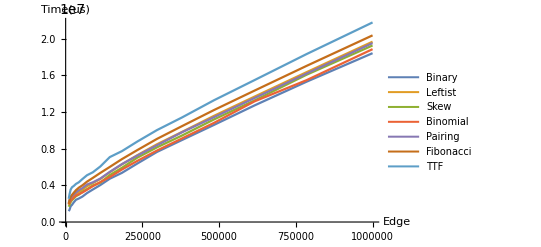

```mathematica
names = {"Binary","Leftist","Skew","Binomial","Pairing","Fibonacci","TTF"};
plots = ListLinePlot[Array[Legended[mat[[#]],names[[#]]]&,7],PlotStyle->Thickness[0.004],AxesLabel->{"Edge","Time(us)"}]
```